```mathematica
Charting`$InteractiveHighlighting=False
```

False

```mathematica
SetOptions[SelectedNotebook[],PrintingStyleEnvironment->"Printout",ShowSyntaxStyles->True]
```

```mathematica
n=25; (* Points to sample along each connection *)
```

```mathematica
Π=N@With[{Γ={0,0,0},X={0,1,0},W={1/2,1,0},L={1/2,1/2,1/2},K={3/4,3/4,0},U={1/4,1,1/4}},{L,K,U,W,Γ,X,W,L,Γ,K,U,X}]; (* The list of high-symmetry points *)
K=Subdivide[#1,#2,n]&@@@Partition[Π,2,1]//Flatten[#,1]&//DeleteAdjacentDuplicates;(* List of n points sampled along each line of the path going through the high-symmetry points, it's literally the points generated by traversing the line, although not in equal steps *)
Length@K (* Total count of the sampling points *)
Graphics3D[{Point[#]&/@K,Line[Π]},Axes->True]
```

276

-Graphics3D-

```mathematica
β=N@{{1,-1,1},{1,1,-1},{-1,1,1}}; (* The basis for the G *)
G=Tuples[Range[-5,5],3].β; (* All possible combinations that give the G points *)
Length@G (* Number of sampled points *)
(* 1BZ represented for a bcc lattice *)
With[{G=Tuples[Range[-2,2],3].β},Show[VoronoiMesh[G,PlotTheme->"Lines",MeshCellStyle->{{3,"Interior"}->Directive[Opacity[1]]}],Graphics3D[{{AbsolutePointSize[7],Red,Point[G]},{Thick,Line[Π]}}],PlotRange->Automatic]]
```

1331

-Graphics3D-

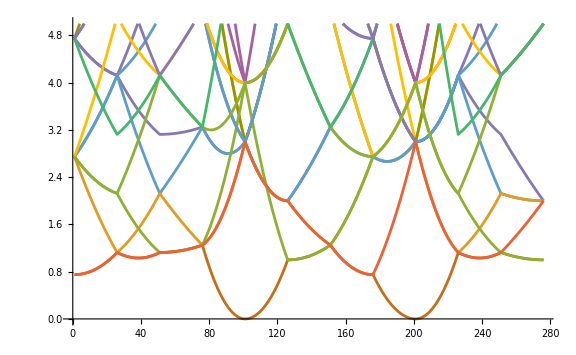

```mathematica
λ=With [{ξ=Tuples[{K,G}]//Partition[#,Length@G]&},Norm[#1-#2]^2&@@@#&/@ξ]//Transpose; (* Energy levels calculated along the path traced in the first Brillouin zone for a bcc lattice *)
ListLinePlot[λ,ImageSize->Large,PlotRange->{0,5}]
```

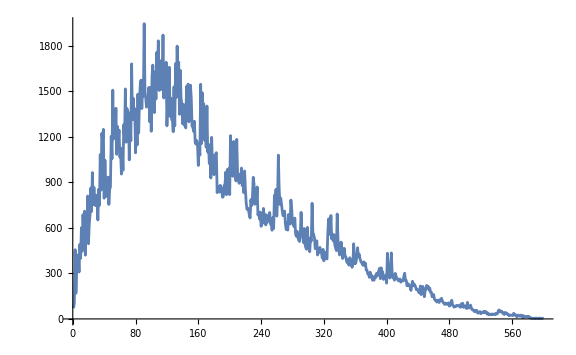

```mathematica
(* Density of states (only somes states) for the free electron *)
BinCounts[Flatten@λ,{0,300,0.5}]//ListLinePlot[#,ImageSize->Large,PlotRange->All]&
```

```mathematica
ζ=With[{G=Tuples[Range[-1,1],3].β},Select[MeshPrimitives[VoronoiMesh[G],3],RegionMember[#,{0,0,0}]&]//First];
```

```mathematica
K=RandomPoint[ζ,10^4];
Graphics3D[{Style[ζ,Opacity[0.7]],Point@K}]
RegionMeasure[ζ]
```

-Graphics3D-

4.

```mathematica
Λ=With [{ξ=Tuples[{K,G}]//Partition[#,Length@G]&},Norm[#1-#2]^2&@@@#&/@ξ]//Transpose;
```

```mathematica
B=BinCounts[Flatten@Λ,{0,50,0.5}];
```

```mathematica
Subscript[B, fit]=NonlinearModelFit[B,a √x,{a},x];
Subscript[B, fit][{"ANOVATable","ParameterTable"}]
```

{ | DF | SS | MS
Model | 1 | 1.54151×10^11 | 1.54151×10^11
Error | 99 | 1.17577×10^7 | 118765.
Uncorrected Total | 100 | 1.54162×10^11 | 
Corrected Total | 99 | 1.71173×10^10 | , | Estimate | Standard Error | t-Statistic | P-Value
a | 5524.93 | 4.84951 | 1139.28 | 1.19964×10^-205}

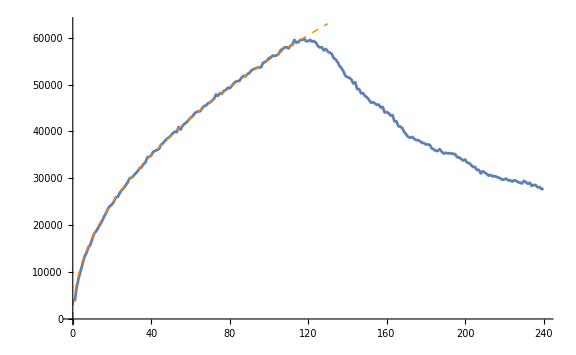

```mathematica
(* Plot of the density of states as a function of energy *)
Show[BinCounts[Flatten@Λ,{0,120,0.5}]//ListLinePlot[#,ImageSize->Large]&,Plot[Subscript[B, fit]["BestFit"],{x,0,130},PlotStyle->{Dashed,Orange,Thick}],PlotRange->All]
```

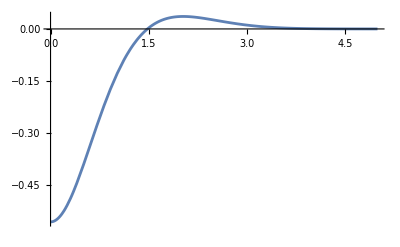

```mathematica
Plot[0.53706/2(r^2-2.19704)/(2.05716Exp[0.48716 r^2]-1),{r,0,5}]
```